```mathematica
(* PRÁCTICA 2 *)
```

```mathematica
(* SESIÓN 2 *)
(* Implementado por: - Lishuang Sun - Fabián Scherle Carboneres *)
(* Ejercicio 1 *)
```

```mathematica
AFDaACUU[afd_List]:=Module[{S,f,Sm,i,j,k,aux},
S = Union[afd[[1]],afd[[2]]]; (* Unión de estados y símbolos del AFD *)
f = afd[[3]]; (* Funciones de transcisión, incluye las transiciones del AFD *)
Sm = afd[[5]]; (* Estados finales del AFD *)

(* Recorremos todos los estados y símbolos del AFD *)
For[i=1,i≤2,i++,
aux = afd[[i]];

(* Calculamos las funciones de transición del AC *)
For[j=1, j≤Length[aux],j++,
For[k=1, k≤Length[aux],k++,
(* Símbolos: f(a,b)=b     Estados: f(q,p)=p *)
AppendTo[f,{aux[[j]],aux[[k]],aux[[k]]} ];
];
];
];

Return[{S,f,Sm}];
]
```

```mathematica
AFDaACUU[{{q,r,p},{a,b},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r}},q,{r}}]
```

{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

```mathematica
(* Ejercicio 2 *)
ACaceptaW[w_List,AC_List, frontera_] := Module[{i,est,trans},
est=frontera; (* Estado de la célula fronteriza *)

(* Recorremos los símbolos de la cadena *)
For[i=1,i≤Length[w],i++,
trans=Cases[AC[[2]],{est,w[[i]],_}]; (* Funciona si AC unidireccional *)
(* En un AFD, un estado con un símbolo puede transitar como máximo a un estado *)
If[Length[trans]== 1,
(* Obtener el siguiente estado *)
est=trans[[1,3]]; ,
(* Si no existe una transición con este símbolo desde el estado actual a otro, el AC no acepta la cadena *)
Return[False];];];
(* Si el último estado al que se ha llegado es un estado final, el AC acepta la cadena *)
Return[MemberQ[AC[[3]],est]];
]
```

```mathematica
ACaceptaW[{a,b,a,a,b},{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}, q]
```

True

```mathematica
(* Ejercicio 3 *)
AFDaACUB[afd_List]:=Module[{acuu,S,fAux,Sm,f,i,j},
acuu = AFDaACUU[afd]; (* Obtenemos el AC unidireccional del AFD *)
S=acuu[[1]]; (* Estados del AC *)
fAux=acuu[[2]]; (* Funciones de transición del AC unidireccional *)
Sm=acuu[[3]]; (* Estados de aceptación del AC *)
f={};

(* Para cada función de transición *)
For[i=1,i≤Length[fAux],i++,
(* Para cada estado del AC *)
For[j=1,j≤Length[S],j++,
(* Insertar el estado como vecino de la derecha de la célula en dicha función de transición *)
AppendTo[f,{fAux[[i,1]],fAux[[i,2]],S[[j]],fAux[[i,3]]}];
];
];
(*  *)
Return[{S, f, Sm}];
]
```

```mathematica
AFDaACUB[{{q,r,p},{a,b},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r}},q,{r}}]
```

{{a,b,p,q,r},{{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b}},{r}}

```mathematica
(* Ejercicio 4 *)
MostrarACaceptaW[w_List,AC_List, frontera_]:=Module[{i,x2,est,trans,configList},
configList={w}; (* w es la cadena de entrada, cada símbolo en una célula definiendo su estado *)
est=frontera; (* Estado de la célula fronteriza *)

(* Recorremos los símbolos de la cadena *)
For[i=1,i≤Length[w],i++,
trans=Cases[AC[[2]],{est,w[[i]],_}]; (* Funciona si AC unidireccional *)
If[Length[trans]== 1,
est=trans[[1,3]];
(* De la última configuración añadida, cambiar el símbolo en la posición i por el nuevo estado *)
x2 = Delete[configList[[1]],i]; PrependTo[configList,Insert[x2,est,i]];,
Return[False];];
];
(* Indica si el AC acepta la cadena w *)
Print[MemberQ[AC[[3]],est]];
(* Visualización de las configuraciones *)
ArrayPlot[configList,ColorRules->{a->Red,b->RGBColor[0.2,0.4,1],q->Yellow,p->RGBColor[0.4,0,0.4],r->RGBColor[0.8,1,0.8]},Mesh->True]
]
```

```mathematica
MostrarACaceptaW[{a,b,a,a,b},{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}, q]
```

True

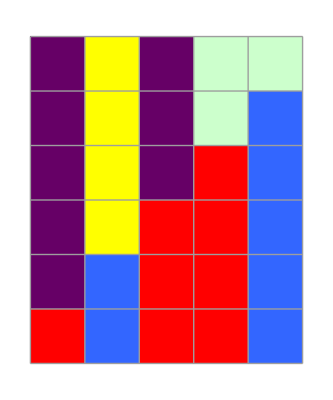

```mathematica
MostrarACaceptaW[{a,b},{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,b,q},{p,a,r},{r,a,r},{r,b,r},{q,q,q},{q,r,r},{q,p,p},{r,q,q},{r,r,r},{r,p,p},{p,q,q},{p,r,r},{p,p,p},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}, q]
```

False